```mathematica
(* This notebook contains examples for the PET-functions
-ActivityB-          calculate the activity of a phase component (exclusive fluids)
-GammaSymbolic-     calculate symbolic expressions for RTln[gamma] and Gex
-GammaBB-           calculate a symbolic expression for RTln[gamma] (Berman & Brown (1985)-formalism)
-MargulesB-          calculate Margules mixing parameters for certain solid solutions
-FluidActivity-     calculate activities in H2O-CO2 or H2O-H2 fluids
*)
(* This top-cell must be run once before any example can be performed.  *)

(* Define the directory,where the PET-files reside (e.g. C:\Eigene Dateien\Pet) and load PET. *)$PetDirectory="C:\Dokumente und Einstellungen\dachsedgar\Eigene Dateien\Pet\Pet7.0";

SetDirectory[$PetDirectory];
DeclarePackage["DEFDAT`",{"Dataset"}];
Dataset[Dataset-> B88];
```

```mathematica
(* _____________________________________________________________________________________________
				Examples for use of the Pet-Function:		-ActivityB-
____________________________________________________________________________________________  *)

(* Example 1: use the PET-function -ActivityB- to calculate a symbolic expression for the ideal activity of a phase-component;
Values of p, t and x are irrelevant in this case   *)

ActivityB[p,t,ann,"",ActivityMode->IdealActivitySymbolic]
```

aid(ann)=XFeM^3*XKA*XOH^2

```mathematica
(* Example 2:use the PET-function-ActivityB-to calculate the ideal activity of a phase-component:(in this case for annite from the biotite data in "hs78b"); 
Values of p,t and x are irrelevant in this case. Note that you must have used CalcFormula["hs78b"] before and Cmp.exe to create the file hs78b.cmp (if you got an error message reload the kernel and do that before trying this example. *)

ActivityB[p,t,ann,x,ActivityMode->IdealActivity,ActivitySampleFile->"hs78b"]
```

{0.0495641,a(ann)=Ideal}

```mathematica
(* Example 3a: use the PET-function -ActivityB- to calculate the activity of a phase-component: 
(in this case for annite from the biotite data in "hs78b.cmp" for P = 5000 bar, T = 500 C); 
Value of x is irrelevant in this case because data are read from the specified sample file *)

ActivityB[5000,500+273,ann,x,ActivitySampleFile->"hs78b"]
```

{0.0617333,a(ann)=BtMcMullin}

```mathematica
(* Example 3b: use the PET-function -ActivityB- to calculate the activity of a phase-component for P = 5000 bar, T = 500 C *)
(* Explicit use of the <x> parameter (data copied from hs78b.cmp) representing {{XK},{XMgM,XFeM,XTiM,XAlM},{XOH}}
To see how the structure of <x> must be, consult the file ACTIVITYBDAT.M *)

x = {{0.7618},{0.3922,0.4022,0.0282,0.1747},{1.}};
ActivityB[5000,500+273,ann,x]
```

{0.0617333,a(ann)=BtMcMullin}

```mathematica
(* Example 4: use the PET-function -ActivityB- to calculate the activity coefficient of a phase-component: 
(in this case for grossular from the garnet data in "hs78b.cmp" for P = 5000 bar, T = 500 C); 
Value of x is irrelevant in this case because data are read from specified sample file *)

ActivityB[5000,500+273,gr,x,ActivitySampleFile->"hs78b",ActivityMode->ActivityCoefficient]
```

{1.86625,y(gr)=GrtBerman}

```mathematica
(* Example 5: use the PET-function -ActivityB- to display the activity model of a phase-component: (in this case for biotite); 
Values of p, t and x are irrelevant in this case *)

ActivityB[p,t,phl,x,ActivityMode->DisplayActivityModel]
```

Activity-model for: bt (one-site basis). Number 2 in data file.

Ideal activity: aid(phl) = XKA XMgM^3 XOH^2

___________________________________

Activity-model 1: BtMcMullin

Site 1 {name, occupancy}: {A,{K}} Ideal

Site 2 {name, occupancy}: {M,{Mg,Fe,Ti,Al}} NonIdeal

Margules parameters displayed as square-matrix: {Mg,Fe,Ti,Al} x {Mg,Fe,Ti,Al}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (0.
0.
0.) | (19621.7
0.
0.) | (25000.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (10307.
0.
0.) | (21240.3
0.
0.)
(19621.7
0.
0.) | (10307.
0.
0.) | (0.
0.
0.) | (0.
0.
0.)
(25000.
0.
0.) | (21240.3
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

Site 3 {name, occupancy}: {,{OH}} Ideal

___________________________________

Activity-model 2: BtBenisek

Site 1 {name, occupancy}: {A,{K}} Ideal

Site 2 {name, occupancy}: {M,{Mg,Fe,Ti,Al}} NonIdeal

Margules parameters displayed as square-matrix: {Mg,Fe,Ti,Al} x {Mg,Fe,Ti,Al}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (7600.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (-9666.67
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.)
(7600.
0.
0.) | (-9666.67
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

Site 3 {name, occupancy}: {,{OH}} Ideal

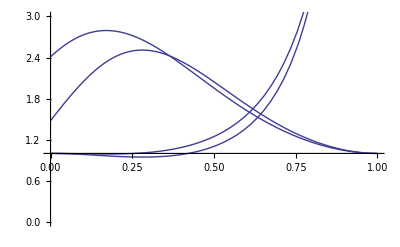

```mathematica
(* Example 6: use the PET-function -ActivityB- to plot one-site normalized activity-coefficients of the pyrope- and grossular phase-components at P = 5000 bar, T = 500 C,  along the grossular - pyrope join, comparing the Margules parameters of Ganguly (1996) and Berman (1990);
This examples does not specify a data file, but mole fractions are directly used in the call to -ActivityB- instead;
As can be seen by inspecting the file "hs78b.fu" or "ACTIVIYBDAT.M", these must be of the form: 
{{"XCa","XMg","XFe","XMn"},{"XAl","XFe3"}}  for garnet.
 *)

(* calculate gammas with Ganguly parameters *)
p1=Plot[ActivityB[5000,773,py,{{1-x,x,0,0},{1,1}},ActivityMode->ActivityCoefficient,ActivityModelGrt->GrtGanguly][[1]]^(1/3),{x,0,1}];
p2=Plot[ActivityB[5000,773,gr,{{1-x,x,0,0},{1,1}},ActivityMode->ActivityCoefficient,ActivityModelGrt->GrtGanguly][[1]]^(1/3),{x,0,1}];
plot1=Show[p1,p2,PlotRange->{{0,1},{0,3}}];

(* calculate gammas with Berman parameters *)
p1=Plot[ActivityB[5000,773,py,{{1-x,x,0,0},{1,1}},ActivityMode->ActivityCoefficient,ActivityModelGrt->GrtBerman][[1]]^(1/3),{x,0,1}];
p2=Plot[ActivityB[5000,773,gr,{{1-x,x,0,0},{1,1}},ActivityMode->ActivityCoefficient,ActivityModelGrt->GrtBerman][[1]]^(1/3),{x,0,1}];
plot2=Show[p1,p2,PlotRange->{{0,1},{0,3}}];

(* display plots together *)
Show[plot1,plot2]
```

```mathematica
(* Example 7: use the PET-function -ActivityB- to calculate activities of garnet phase-components 
for garnet analyses from file "pet2". *)

(* calculate the mineral formulae *)
file = "pet2";
{oxides,analyses,oxygens,dataset,date} = CalcFormula[file,  CalcFormulaMode->{}];
(* loop through the mineral analyses and for all garnet analyses calculate the activity of garnet-phase components for predefined P and T. Data are saved in the variables xxfe, xxmg, xxca, xxmn, aalm, apy, agr for further use. *) 
(* define P, T and garnet activity model  *)
```

Message from -CalcFormula-: creating file "pet2.fu".

```mathematica
p = 7500; t = 500+273.15; 
model = GrtGangulySaxena;
(* save data in the variables xxfe, xxmg, xxca, xxmn, aalm, apy, agr  *)
xxfe = {}; xxmg = {}; xxca = {}; xxmn = {}; aalm = {}; apy = {}; agr = {};
Print["Calculating garnet activities for P = ",p," [bar], T = ",t-273.15," [C] from file: ",file];
Print["Garnet activity model: ",model,"\n"];
(* loop *)
For[i=1,i<Dimensions[analyses][[1]],i++,
If[ToString[analyses[[i,1]]]== "grt",
 {xca,xmg,xfe,xmn}= Last[analyses[[i]]][[2,2,1]];
xxfe = Append[xxfe,xfe]; xxmg = Append[xxmg,xmg];xxca = Append[xxca,xca]; xxmn = Append[xxmn,xmn];
aalm = Append[aalm,ActivityB[p,t,alm,Last[analyses[[i]]][[2,2]],ActivityModelGrt->model][[1]]];
apy = Append[apy,ActivityB[p,t,py,Last[analyses[[i]]][[2,2]],ActivityModelGrt->model][[1]]];
agr = Append[agr,ActivityB[p,t,gr,Last[analyses[[i]]][[2,2]],ActivityModelGrt->model][[1]]];
 Print["Analysis ",i,": XFe = ",xfe,", XMg = ",xmg,", XCa = ",xca,", XMn = ",xmn];
Print["            a(Alm) = ",Last[aalm],", a(Py) = ",Last[apy],", a(Gr) = ",Last[agr]];
  ];
]
```

Calculating garnet activities for P = 7500 [bar], T = 500. [C] from file: pet2

Garnet activity model: GrtGangulySaxena

Analysis 21: XFe = 0.62989, XMg = 0.11751, XCa = 0.23784, XMn = 0.01476

a(Alm) = 0.168711, a(Py) = 0.0976364, a(Gr) = 0.0372874

Analysis 22: XFe = 0.64373, XMg = 0.11477, XCa = 0.22777, XMn = 0.01373

a(Alm) = 0.181936, a(Py) = 0.0959501, a(Gr) = 0.0309361

Analysis 23: XFe = 0.63457, XMg = 0.10767, XCa = 0.23852, XMn = 0.01925

a(Alm) = 0.169512, a(Py) = 0.0882256, a(Gr) = 0.0365451

Analysis 24: XFe = 0.63715, XMg = 0.1029, XCa = 0.24237, XMn = 0.01758

a(Alm) = 0.168826, a(Py) = 0.0829554, a(Gr) = 0.0388121

Analysis 25: XFe = 0.63195, XMg = 0.0938, XCa = 0.25549, XMn = 0.01876

a(Alm) = 0.158738, a(Py) = 0.0718051, a(Gr) = 0.0476218

Analysis 26: XFe = 0.63609, XMg = 0.08776, XCa = 0.26128, XMn = 0.01487

a(Alm) = 0.158133, a(Py) = 0.064554, a(Gr) = 0.0523223

Analysis 27: XFe = 0.6429, XMg = 0.07974, XCa = 0.25804, XMn = 0.01932

a(Alm) = 0.162449, a(Py) = 0.0560951, a(Gr) = 0.0486269

Analysis 28: XFe = 0.6431, XMg = 0.07283, XCa = 0.26026, XMn = 0.02381

a(Alm) = 0.160743, a(Py) = 0.0480911, a(Gr) = 0.0496268

Analysis 29: XFe = 0.64947, XMg = 0.07403, XCa = 0.25557, XMn = 0.02092

a(Alm) = 0.166928, a(Py) = 0.0499327, a(Gr) = 0.0461125

Analysis 30: XFe = 0.64494, XMg = 0.07082, XCa = 0.26779, XMn = 0.01646

a(Alm) = 0.158565, a(Py) = 0.0451874, a(Gr) = 0.0569074

Analysis 31: XFe = 0.65134, XMg = 0.07005, XCa = 0.26214, XMn = 0.01647

a(Alm) = 0.16482, a(Py) = 0.0449234, a(Gr) = 0.0517575

Analysis 32: XFe = 0.64354, XMg = 0.0712, XCa = 0.26822, XMn = 0.01704

a(Alm) = 0.157588, a(Py) = 0.0455417, a(Gr) = 0.0572653

Analysis 33: XFe = 0.6607, XMg = 0.07533, XCa = 0.24521, XMn = 0.01877

a(Alm) = 0.179304, a(Py) = 0.0523496, a(Gr) = 0.0385656

Analysis 34: XFe = 0.64431, XMg = 0.07262, XCa = 0.26358, XMn = 0.01948

a(Alm) = 0.160124, a(Py) = 0.0475668, a(Gr) = 0.0528799

Analysis 35: XFe = 0.60269, XMg = 0.06275, XCa = 0.29845, XMn = 0.03611

a(Alm) = 0.124005, a(Py) = 0.032912, a(Gr) = 0.086619

Analysis 36: XFe = 0.43975, XMg = 0.03686, XCa = 0.38613, XMn = 0.13726

a(Alm) = 0.0516485, a(Py) = 0.00632527, a(Gr) = 0.182144

Analysis 37: XFe = 0.44842, XMg = 0.04012, XCa = 0.3731, XMn = 0.13836

a(Alm) = 0.0547277, a(Py) = 0.00836669, a(Gr) = 0.160955

Analysis 38: XFe = 0.43808, XMg = 0.03697, XCa = 0.38624, XMn = 0.13871

a(Alm) = 0.051238, a(Py) = 0.00635931, a(Gr) = 0.181481

Analysis 39: XFe = 0.45181, XMg = 0.03681, XCa = 0.38044, XMn = 0.13094

a(Alm) = 0.0549497, a(Py) = 0.00656662, a(Gr) = 0.176945

Analysis 40: XFe = 0.45054, XMg = 0.04074, XCa = 0.36961, XMn = 0.13911

a(Alm) = 0.0555114, a(Py) = 0.00884804, a(Gr) = 0.155462

Analysis 41: XFe = 0.45437, XMg = 0.03815, XCa = 0.37447, XMn = 0.133

a(Alm) = 0.0560451, a(Py) = 0.0074033, a(Gr) = 0.166393

Analysis 42: XFe = 0.45906, XMg = 0.04835, XCa = 0.37355, XMn = 0.11904

a(Alm) = 0.0585405, a(Py) = 0.0128701, a(Gr) = 0.166071

Analysis 43: XFe = 0.48329, XMg = 0.0452, XCa = 0.35392, XMn = 0.11759

a(Alm) = 0.0663804, a(Py) = 0.012428, a(Gr) = 0.140393

Analysis 44: XFe = 0.46171, XMg = 0.03578, XCa = 0.37148, XMn = 0.13102

a(Alm) = 0.0579281, a(Py) = 0.00648746, a(Gr) = 0.164217

Analysis 45: XFe = 0.46838, XMg = 0.03715, XCa = 0.35602, XMn = 0.13845

a(Alm) = 0.060886, a(Py) = 0.00772313, a(Gr) = 0.138753

Analysis 46: XFe = 0.46447, XMg = 0.03843, XCa = 0.35305, XMn = 0.14405

a(Alm) = 0.0600515, a(Py) = 0.00846662, a(Gr) = 0.132344

Analysis 47: XFe = 0.46092, XMg = 0.03647, XCa = 0.37735, XMn = 0.12525

a(Alm) = 0.0574749, a(Py) = 0.00657556, a(Gr) = 0.175295

Analysis 48: XFe = 0.46353, XMg = 0.03789, XCa = 0.37949, XMn = 0.11909

a(Alm) = 0.0582222, a(Py) = 0.00713258, a(Gr) = 0.180784

Analysis 49: XFe = 0.453, XMg = 0.03693, XCa = 0.38788, XMn = 0.12219

a(Alm) = 0.0549511, a(Py) = 0.00634887, a(Gr) = 0.192817

Analysis 50: XFe = 0.44765, XMg = 0.03829, XCa = 0.38813, XMn = 0.12594

a(Alm) = 0.0537381, a(Py) = 0.00688696, a(Gr) = 0.19021

Analysis 51: XFe = 0.45695, XMg = 0.03508, XCa = 0.37966, XMn = 0.1283

a(Alm) = 0.0561441, a(Py) = 0.00589387, a(Gr) = 0.178142

Analysis 52: XFe = 0.44159, XMg = 0.03676, XCa = 0.3877, XMn = 0.13395

a(Alm) = 0.0520489, a(Py) = 0.00623569, a(Gr) = 0.186282

Analysis 53: XFe = 0.45963, XMg = 0.04338, XCa = 0.34639, XMn = 0.15061

a(Alm) = 0.0595057, a(Py) = 0.0115471, a(Gr) = 0.12016

Analysis 54: XFe = 0.44379, XMg = 0.04016, XCa = 0.37231, XMn = 0.14374

a(Alm) = 0.0535277, a(Py) = 0.00839505, a(Gr) = 0.157477

Analysis 55: XFe = 0.43541, XMg = 0.03681, XCa = 0.37093, XMn = 0.15685

a(Alm) = 0.0510044, a(Py) = 0.00683197, a(Gr) = 0.151773

Analysis 56: XFe = 0.43517, XMg = 0.03779, XCa = 0.36882, XMn = 0.15822

a(Alm) = 0.0511088, a(Py) = 0.00735636, a(Gr) = 0.147947

Analysis 57: XFe = 0.43395, XMg = 0.03868, XCa = 0.36485, XMn = 0.16253

a(Alm) = 0.0509986, a(Py) = 0.00793103, a(Gr) = 0.140744

Analysis 58: XFe = 0.43523, XMg = 0.03781, XCa = 0.37928, XMn = 0.14768

a(Alm) = 0.0508147, a(Py) = 0.00696474, a(Gr) = 0.166616

Analysis 59: XFe = 0.42083, XMg = 0.03712, XCa = 0.36224, XMn = 0.17981

a(Alm) = 0.047458, a(Py) = 0.00721002, a(Gr) = 0.131918

Analysis 60: XFe = 0.44541, XMg = 0.03924, XCa = 0.31023, XMn = 0.20512

a(Alm) = 0.0566108, a(Py) = 0.0104706, a(Gr) = 0.071615

Analysis 61: XFe = 0.46663, XMg = 0.04222, XCa = 0.30059, XMn = 0.19055

a(Alm) = 0.0645495, a(Py) = 0.0130391, a(Gr) = 0.0652454

Analysis 62: XFe = 0.45734, XMg = 0.03905, XCa = 0.32882, XMn = 0.17479

a(Alm) = 0.0593659, a(Py) = 0.00973608, a(Gr) = 0.0950808

Analysis 63: XFe = 0.55273, XMg = 0.04392, XCa = 0.31567, XMn = 0.08768

a(Alm) = 0.0956912, a(Py) = 0.0143985, a(Gr) = 0.0986543

Analysis 64: XFe = 0.59873, XMg = 0.04761, XCa = 0.31082, XMn = 0.04283

a(Alm) = 0.116998, a(Py) = 0.0180316, a(Gr) = 0.102003

Analysis 65: XFe = 0.60817, XMg = 0.04756, XCa = 0.30993, XMn = 0.03435

a(Alm) = 0.121581, a(Py) = 0.0181633, a(Gr) = 0.102721

Analysis 66: XFe = 0.61394, XMg = 0.0515, XCa = 0.30941, XMn = 0.02515

a(Alm) = 0.12482, a(Py) = 0.0215843, a(Gr) = 0.103781

Analysis 67: XFe = 0.63035, XMg = 0.06057, XCa = 0.2921, XMn = 0.01698

a(Alm) = 0.139766, a(Py) = 0.0317831, a(Gr) = 0.0824831

Analysis 68: XFe = 0.63979, XMg = 0.06221, XCa = 0.28373, XMn = 0.01427

a(Alm) = 0.148197, a(Py) = 0.0343652, a(Gr) = 0.0731823

Analysis 69: XFe = 0.63813, XMg = 0.06672, XCa = 0.27733, XMn = 0.01781

a(Alm) = 0.150254, a(Py) = 0.0396907, a(Gr) = 0.0659265

Analysis 70: XFe = 0.64022, XMg = 0.06912, XCa = 0.27148, XMn = 0.01918

a(Alm) = 0.15404, a(Py) = 0.0428899, a(Gr) = 0.0600144

Analysis 71: XFe = 0.64452, XMg = 0.06628, XCa = 0.27139, XMn = 0.0178

a(Alm) = 0.156303, a(Py) = 0.0398587, a(Gr) = 0.0599566

Analysis 72: XFe = 0.64125, XMg = 0.06818, XCa = 0.27097, XMn = 0.0196

a(Alm) = 0.154741, a(Py) = 0.0419239, a(Gr) = 0.0594314

Analysis 73: XFe = 0.6395, XMg = 0.0709, XCa = 0.26924, XMn = 0.02037

a(Alm) = 0.15471, a(Py) = 0.0450573, a(Gr) = 0.0578351

Analysis 74: XFe = 0.64435, XMg = 0.08685, XCa = 0.25312, XMn = 0.01569

a(Alm) = 0.166463, a(Py) = 0.0645813, a(Gr) = 0.0455101

Analysis 75: XFe = 0.63391, XMg = 0.09503, XCa = 0.25541, XMn = 0.01565

a(Alm) = 0.160227, a(Py) = 0.0731288, a(Gr) = 0.0479413

```mathematica
(* _____________________________________________________________________________________________
				Example(s) for use of the Pet-Function(s):		-GammaSymbolic-
																      -GammaBB-
____________________________________________________________________________________________  *)

(* The PET-functions -GammaSymbolic- and -GammaBB- have been copied from ActivityB.M into this cell and are named
-GammaSymbolic1- and -GammaBB1- here and are used in some examples below. This avoids longer outputs with contexts as with use of the analogous functions in ActivityB.M. Quit and reload the Kernel, run top-cell and this cell before trying the examples below. *)
  
GammaSymbolic1[c_,comp_,model_]:=Block[{gex=0,gex1,i,j,k,x,n,q,gexn,gamma,sumn,w},
Off[Part::partd];
(* note:model 1 and 2 are identical,if binary W's are interchanced,e.g.w[[1,1,2]]=w[[2,1]],etc.,ternary w's are identical *)
 If[model==1,(* setup expression for Gex:Berman and Brown,1984,eq.9 *)
For[i=1,i≤(c-1),i++,
For[j=i,j≤c,j++,
For[k=j,k≤c,k++,If[k≠i,gex=gex+w[[i,j,k]]x[[i]]x[[j]]x[[k]]]]]];];

If[model==2,(* setup expression for Gex:Wohl equation expanded according to Jackson,1989,eq.6 *)
For[i=1,i≤(c-1),i++,
For[j=2,j≤c,j++,If[i<j,gex=gex+x[[i]]x[[j]](x[[i]]w[[j,i]]+x[[j]]w[[i,j]])]]];
	For[i=1,i≤(c-2),i++,For[j=2,j≤(c-1),j++,
	For[k=3,k≤c,k++,If[i<j&&j<k,gex=gex+x[[i]]x[[j]]x[[k]]q[[i,j,k]]]]]];];

If[model==3,(* setup expression for Gex:Meyre et al.,1997,eq.3 *)For[i=1,i≤(c-1),i++,For[j=i,j≤c,j++,For[k=j,k≤c,k++,If[k≠i,If[k==i||k==j||j==i,gex=gex+w[[i,j,k]]x[[i]]x[[j]]x[[k]]/(x[[i]]+x[[k]]);]]]]];];

gex1=gex;
sumn=Sum[n[[j]],{j,1,c}];
For[i=1,i≤c,i++,gex=gex/.x[[i]]->n[[i]]/sumn];(* replace mole fractions by moles *)
gexn=gex sumn;(* symbolic gex for all moles *)
gamma=D[gexn,n[[comp]]];(* RTln(gamma) *)
If[model==1||model==2||model==3,gamma=gamma/.{sumn->1,n->x}];
Return[{gamma,gex1}];
On[Part::partd];]

GammaBB1[m_,c_,w_,x_]:=GammaBB[m,c]=Block[{nrtlny=0,i,j,k,qm,x,w,p=3},(* nsRTlny(m) according to Berman & Brown (1985,eq.22):third-degree polynomial asymmetric excess model for the m_th out of c cations on site s of component j.Identical results are calculated with the PET-function-GammaSymbolic- *)
Off[Part::partd];
For[i=1,i≤(c-1),i++,
For[j=i,j≤c,j++,
For[k=j,k≤c,k++,If[k≠i,qm=Dimensions[Position[{i,j,k},m]][[1]];
nrtlny=nrtlny+w[[i,j,k]](qm x[[i]]x[[j]]x[[k]]/x[[m]]+(1-p)x[[i]]x[[j]]x[[k]])]]]];
Return[nrtlny];
On[Part::partd];]
```

```mathematica
(* Example 8:  use the PET-function -GammaSymbolic1- (located in the cell above)to calculate a symbolic expression for RTln(gamma) 
(first element of the return-list) and for Gex (2nd element of the return-list) for a binary system for 
component 1 using the formalism of Berman and Brown (1984) for G(ex) *)

Clear[w];Clear[x];
{gamma1,gex} = GammaSymbolic1[2,1,1]
```

{2 x⟦1⟧ x⟦2⟧ w⟦1,1,2⟧-2 x⟦1⟧^2 x⟦2⟧ w⟦1,1,2⟧+x⟦2⟧^2 w⟦1,2,2⟧-2 x⟦1⟧ x⟦2⟧^2 w⟦1,2,2⟧,x⟦1⟧^2 x⟦2⟧ w⟦1,1,2⟧+x⟦1⟧ x⟦2⟧^2 w⟦1,2,2⟧}

```mathematica
(* Example 9a:  use the PET-function -GammaBB1- (located two cells above)to calculate a 
symbolic expression for RTln(gamma)using the formalism of Berman and Brown (1984) for RTln(gamma) *)

gamma2 =GammaBB1[1,2,w,x]
(* both results of Examples 1 and 2 are identical, therefore their difference is zero *)
Simplify[gamma1-gamma2]
```

(2 x⟦1⟧ x⟦2⟧-2 x⟦1⟧^2 x⟦2⟧) w⟦1,1,2⟧+(x⟦2⟧^2-2 x⟦1⟧ x⟦2⟧^2) w⟦1,2,2⟧

0

```mathematica
(* Example 9b: use the PET-function -GammaBB- to calculate a numerical value for RTln(gamma)and 
gamma of the grossular component in garnet from sample "hs78b" for P = 5000 bar, T = 500 C, using the formalism of Berman and Brown (1984) *)
(* copied from ACTIVITYDAT.M, the list <marg> contains the Berman (1990) Margules parameters of garnet 
in a square matrix (order: Ca, Mg, Fe, Mn)  *) 

Clear[w]; Clear[x];
marg={{{{0,0,0},{21560/3,18.79/3,0.1/3},{20320/3,5.08/3,0.17/3},{0,0,0}},{{69200/3,18.79/3,0.1/3},{0,0,0},{230/3,0,0.01/3},{0,0,0}},{{2620/3,5.08/3,0.09/3},{3720/3,0,0.06/3},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}},{{{1,2,3},{0,0,0}}}};
MatrixForm[marg[[1]]] (* display Margules parameters in Matrix-form *)
CalcFormula["hs78b",CalcFormulaMode->{}];
w=MargulesB[5000,500+273,marg,4] (* calculate three-dimensional W's (three indices) at P and T, appropriate for the Berman / Brown formalism *)
x = ExtractSampleDatB["grt","hs78b"][[1]] (* extract site fractions of Ca, Mg, Fe and Mn in garnet from the file "hs78b" *)
rtlny =GammaBB[1,4,w,x] (* Ca is cation 1 out of 4 mixing cations on this site of garnet *)
gamma = (Exp[rtlny/(8.3143*773)])^3       (* results are identical to example 8  *)
```

((0
0
0) | (21560/3
6.26333
0.0333333) | (20320/3
1.69333
0.0566667) | (0
0
0)
(69200/3
6.26333
0.0333333) | (0
0
0) | (230/3
0
0.00333333) | (0
0
0)
(2620/3
1.69333
0.03) | (1240
0
0.02) | (0
0
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0))

Message from -CalcFormula-: creating file "hs78b.fu".

{{{0,2511.78,5747.72,0},{0,18391.8,13899.5,10451.8},{0,0,-285.613,2731.05},{0,0,0,0}},{{0,0,0,0},{0,0,93.3333,0},{0,0,1340.,716.667},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

{0.0254,0.0934,0.7691,0.1121}

1336.65

1.86625

```mathematica
(* __________________________________________________________________________________________
	Example for use of the Pet-Functions: 		-MargulesB- in combination with -GammaSymbolic-
________________________________________________________________________________________ *)
(* Example 10: calculate G(mix) for the grossular - pyrope join at 1 bar, 500 C comparing the binary mixing models of Berman & Aranovich (1996), Ganguly et al. (1996) and Mukhopadhyay et al. (1997); 
This plot reproduces Fig. 1a of Holdaway, (2000): Am Min 85: 881-892 *)
(* First display the activity models of garnet *)

ActivityB[p,t,py,"",ActivityMode->DisplayActivityModel]
```

Activity-model for: grt (one-site basis). Number 1 in data file.

Ideal activity: aid(py) = XMgC^3

___________________________________

Activity-model 1: GrtBerman

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (7186.67
6.26333
0.0333333) | (6773.33
1.69333
0.0566667) | (0.
0.
0.)
(23066.7
6.26333
0.0333333) | (0.
0.
0.) | (76.6667
0.
0.00333333) | (0.
0.
0.)
(873.333
1.69333
0.03) | (1240.
0.
0.02) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

___________________________________

Activity-model 2: GrtHoldaway

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (8586.33
4.29
0.0466667) | (6644.
3.22333
0.045) | (475.
0.
0.0216667)
(22038.
6.32667
0.0226667) | (0.
0.
0.) | (-1890.67
-1.99667
-0.0113333) | (13749.7
7.67
0.013)
(-434.667
-0.113333
0.0133333) | (3874.
1.83333
0.0166667) | (0.
0.
0.) | (620.
0.
0.00733333)
(475.
0.
0.0216667) | (13749.7
7.67
0.013) | (620.
0.
0.00733333) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{2466,0,0}}}

___________________________________

Activity-model 3: GrtMukhopadhyay

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (4768.67
0.83
0.0466667) | (5842.
4.83667
0.045) | (0.
0.
0.)
(21727.3
6.94
0.0226667) | (0.
0.
0.) | (-8055.33
-7.36333
-0.0113333) | (0.
0.
0.)
(-6037.67
-5.17
0.0133333) | (7421.67
4.13333
0.0166667) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{2466,0,0}}}

___________________________________

Activity-model 4: GrtBermanAranovich

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (11156.7
6.26333
0.0576667) | (7317.13
3.14333
0.0566667) | (0.
0.
0.)
(22760.
6.26333
0.012) | (0.
0.
0.) | (1688.17
1.37
0.00333333) | (0.
0.
0.)
(3860.5
3.14333
0.03) | (2083.03
1.37
0.02) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

___________________________________

Activity-model 5: GrtGanguly

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (9834.
5.78
0.058) | (6773.
1.69
0.03) | (6773.
1.69
0.03)
(21627.
5.78
0.012) | (0.
0.
0.) | (695.
0.
0.) | (12083.
7.67
0.03)
(873.
1.69
0.) | (2117.
0.
0.07) | (0.
0.
0.) | (539.
0.
0.01)
(873.
1.69
0.) | (12083.
7.67
0.04) | (539.
0.
0.04) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

___________________________________

Activity-model 6: GrtDachs

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (2292.07
2.08333
0.0543333) | (3506.4
0.893333
0.0331667) | (0.
0.
0.)
(7327.53
2.08333
-0.00443333) | (0.
0.
0.) | (75.4
0.
-0.0000233333) | (0.
0.
0.)
(-945.467
0.150333
0.0205) | (379.3
0.
0.00733333) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

___________________________________

Activity-model 7: GrtLal

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (4184.
6.276
0.) | (4560.56
0.
0.) | (0.
0.
0.)
(16932.6
6.276
0.) | (0.
0.
0.) | (-5255.1
-4.184
0.) | (0.
0.
0.)
(-3025.03
-1.38909
0.) | (12049.9
7.1128
0.) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{-18819.6,-6.34294,0}}}

___________________________________

Activity-model 8: GrtGangulySaxena

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (4184.
6.276
0.) | (19330.1
6.276
0.) | (0.
0.
0.)
(16932.6
6.276
0.) | (0.
0.
0.) | (836.8
0.
0.) | (12552.
0.
0.)
(-2635.92
6.276
0.) | (10460.
0.
0.) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (12552.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{-22175.2,0,0}},{{1,2,4},{-6372.23,0,0}},{{1,3,4},{10983.,0,0}},{{2,3,4},{-4811.6,0,0}}}

___________________________________

Activity-model 9: GrtNewtonHaselton

Site 1 {name, occupancy}: {C,{Ca,Mg,Fe,Mn}} NonIdeal

Margules parameters displayed as square-matrix: {Ca,Mg,Fe,Mn} x {Ca,Mg,Fe,Mn}

Each matrix-element is {WH, WS, WV} on a one-site basis. Units: J, bar, mol.

((0.
0.
0.) | (13807.2
6.276
0.) | (0.
0.
0.) | (0.
0.
0.)
(13807.2
6.276
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.))

Ternary parameter(s): {{{1,2,3},{0,0,0}}}

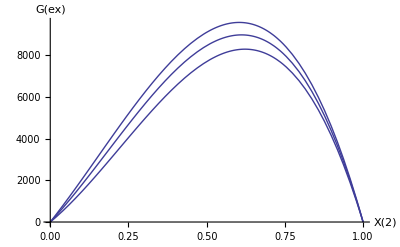

```mathematica
(* Example 10 continued: *)
(* this shows that grt is number 1 in the data file, that the activity models of Mukhopadhyay et al. (1997),Berman & Aranovich (1996) and Ganguly et al. (1996) are models 3, 4 and 5 and that there are four components in the order {Ca, Mg, Fe, Mn}; 
Thus X(2) is X(py);
G(ex) is calculated for a 4 component-mixture and X(3) and X(4) are then set to 0;
run 2nd cell with source-code of -GammaSymbolic1- before running this example *)

Clear[w]; Clear[x];
dat=LoadActivityData["ACTIVITYBDAT.m"]; (* load the activity-data-file containing the Margules parameters  *)

(* pick out the models: the 2nd index is alway 3  *)
model3 = dat[[1,3,3]];
model4 = dat[[1,3,4]];
model5 = dat[[1,3,5]];

p=1; t=500+273.15; c = 4; Clear[x];
(* calculate the Margules parameters for P and T for the 1st model: the index [[2,1]] is required: the first index is alway 2, the 2nd index 1 indicates site 1 (the only site on which mixing occurs in the case of garnet. *)
w=MargulesB[p,t,model3[[2,1]],c];
{gamma1,gex} = GammaSymbolic1[4,1,1]; (* gex is assigned the G(ex) function for a quaternary garnet  *)
(* replace in the gex-expression x[[1]] by (1-x2), x[[2]] by x2, set x[[3]] and x[[4]] = 0  *)
gex = gex/.{x[[1]]->(1-x2),x[[2]]->x2,x[[3]]->0,x[[4]]->0};
p1=Plot[3gex,{x2,0,1},DisplayFunction->Identity]; (* create the 1st plot, but supress plotting  *)

(* calculate the Margules parameters for P and T for the 2nd model: the index [[2,1]] is required. *)
w=MargulesB[p,t,model4[[2,1]],c];
{gamma1,gex} = GammaSymbolic1[4,1,1]; (* gex is assigned the G(ex) function for a quaternary garnet  *)
(* replace in the gex-expression x[[1]] by (1-x2), x[[2]] by x2, set x[[3]] and x[[4]] = 0  *)
gex = gex/.{x[[1]]->(1-x2),x[[2]]->x2,x[[3]]->0,x[[4]]->0};
p2=Plot[3gex,{x2,0,1},DisplayFunction->Identity]; (* create the 2nd plot  *)

(* calculate the Margules parameters for P and T for the 3rd model: the index [[2,1]] is required. *)
w=MargulesB[p,t,model5[[2,1]],c];
{gamma1,gex} = GammaSymbolic1[4,1,1]; (* gex is assigned the G(ex) function for a quaternary garnet  *)
(* replace in the gex-expression x[[1]] by (1-x2), x[[2]] by x2, set x[[3]] and x[[4]] = 0  *)
gex = gex/.{x[[1]]->(1-x2),x[[2]]->x2,x[[3]]->0,x[[4]]->0};
p3=Plot[3gex,{x2,0,1},DisplayFunction->Identity]; (* create the 3rd plot  *)

(* show all three plots together *)
Show[p1,p2,p3,DisplayFunction->$DisplayFunction,PlotRange->All,AxesLabel->{"X(2)","G(ex)"}]
```

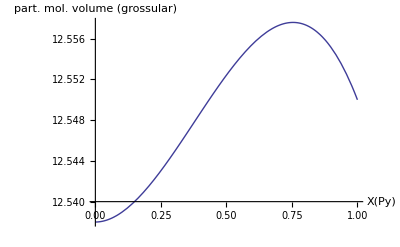

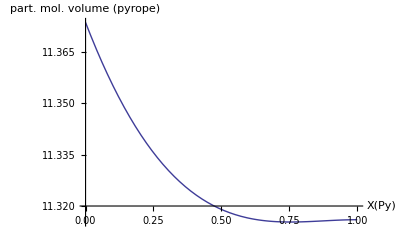

```mathematica
(* Example 11: calculate the partial molar volumes of the grossular- and pyrope component along the grossular - pyrope join,
using the mixing model of Berman & Aranovich (1996).
Note that the component order is: 
1 = grossular, 2 = pyrope, 3 = almandine,  4 = spessartine: -> X(2) is X(py);
  V(ex) is calculated for a 4 component-mixture and X(3) and X(4) are then set to 0
*)

Clear[w]; Clear[x];
dat=LoadActivityData["ACTIVITYBDAT.m"]; (* load the activity-data-file containing the Margules parameters  *)
(* pick out the Berman-Aranovich model (model 4) *)
model4 = dat[[1,3,4]]; c = 4;
w=MargulesB[p,t,model4[[2,1]],c,MargulesMode->WV];
{gamma1,vex} = GammaSymbolic1[4,1,1]; (* vex is assigned the V(ex) function for a quaternary garnet  *)
(* replace in the V(ex)-expression x[[1]] by (1-x2), x[[2]] by x2, set x[[3]] and x[[4]] = 0  *)
vex = vex/.{x[[1]]->(1-x2),x[[2]]->x2,x[[3]]->0,x[[4]]->0}; 
vo2 = MinDat[py][[2,5]];vo1 = MinDat[gr][[2,5]]; (* volume of the end-members from Berman data set *)
vmech = (1-x2)vo1 + x2 vo2; (* molar volume of mechanical mixture *)
v = vmech + vex; (* total molar volume of mixture  *)
vp1 = v - D[v,x2] x2; (* partial molar volume of grossular component  *)
vp2 = v + D[v,x2] (1-x2); (* partial molar volume of pyrope component  *)
p1a=Plot[vp1,{x2,0,1},PlotRange->All,AxesLabel->{"X(Py)","part. mol. volume (grossular)"}]
p1b=Plot[vp2,{x2,0,1},PlotRange->All,AxesLabel->{"X(Py)","part. mol. volume (pyrope)"}]
```

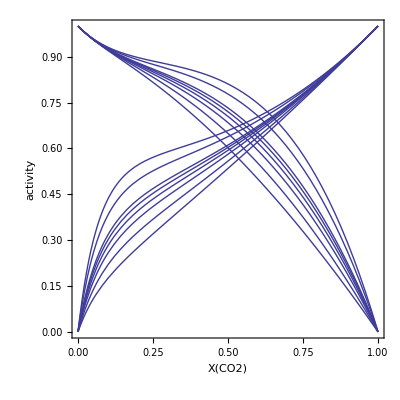

```mathematica
(* _____________________________________________________________________________________________
		Examples for use of the Pet-Function:	-ActivityB- in calculating fluid properties
____________________________________________________________________________________________  *)

(* Example 12: use the PET-function -ActivityB- to calculate activities in H2O-CO2 fluids at P and T.
This example uses the Kerrick & Jacobs (1981) model and reproduces their Fig.12 *)

t = 500+273.15;
SetOptions[FluidActivity,FluidActivityModel->KerrickJacobs81,FluidSystem->H2OCO2];
p1a=Plot[ActivityB[1000,t,h2o,1-x][[1]],{x,0,1}];
p1b=Plot[ActivityB[1000,t,co2,x][[1]],{x,0,1}];
p2a=Plot[ActivityB[2000,t,h2o,1-x][[1]],{x,0,1}];
p2b=Plot[ActivityB[2000,t,co2,x][[1]],{x,0,1}];
p4a=Plot[ActivityB[4000,t,h2o,1-x][[1]],{x,0,1}];
p4b=Plot[ActivityB[4000,t,co2,x][[1]],{x,0,1}];
p6a=Plot[ActivityB[6000,t,h2o,1-x][[1]],{x,0,1}];
p6b=Plot[ActivityB[6000,t,co2,x][[1]],{x,0,1}];
p8a=Plot[ActivityB[8000,t,h2o,1-x][[1]],{x,0,1}];
p8b=Plot[ActivityB[8000,t,co2,x][[1]],{x,0,1}];
p10a=Plot[ActivityB[10000,t,h2o,1-x][[1]],{x,0,1}];
p10b=Plot[ActivityB[10000,t,co2,x][[1]],{x,0,1}];
p20a=Plot[ActivityB[20000,t,h2o,1-x][[1]],{x,0,1}];
p20b=Plot[ActivityB[20000,t,co2,x][[1]],{x,0,1}];
p30a=Plot[ActivityB[30000,t,h2o,1-x][[1]],{x,0,1}];
p30b=Plot[ActivityB[30000,t,co2,x][[1]],{x,0,1}];
plot1=Show[p1a,p1b,p2a,p2b,p4a,p4b,p6a,p6b,p8a,p8b,p10a,p10b,p20a,p20b,p30a,p30b,
AspectRatio->1,Frame->True,PlotRange->{{0,1},{0,1}},FrameLabel->{"X(CO2)","activity"}]
```

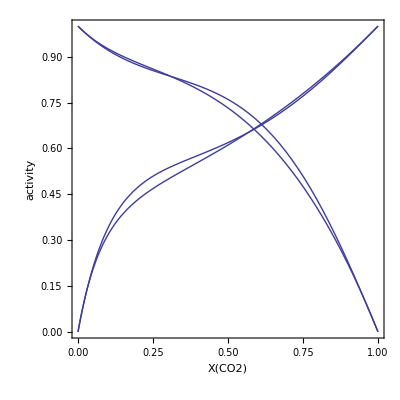

```mathematica
(* Example 13: use the PET-function -ActivityB- to calculate activities in H2O-CO2 fluids at P and T.
This example uses the Powell & Holland (1985) model, which is a Margules-fit to Kerrick & Jakobs (1981), and compares the results with the example before for P = 10 kbar *)

p = 10000; t = 500+273.15;
SetOptions[FluidActivity,FluidActivityModel->PowellHolland85,FluidSystem->H2OCO2];
p1=Plot[ActivityB[p,t,h2o,1-x][[1]],{x,0,1}];
p2=Plot[ActivityB[p,t,co2,x][[1]],{x,0,1}];
plot2=Show[p1,p2,p10a,p10b,AspectRatio->1,Frame->True,PlotRange->{{0,1},{0,1}},FrameLabel->{"X(CO2)","activity"}]
```

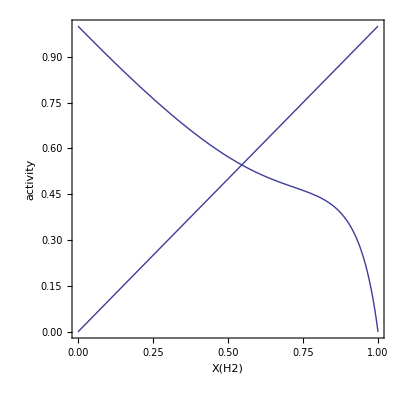

```mathematica
(* Example 14: use the PET-function -ActivityB- to calculate activities in H2O-H2 fluids at P and T *)

p = 5000; t = 500+273.15;
SetOptions[FluidActivity,FluidSystem->H2OH2];
p1=Plot[ActivityB[p,t,h2o,1-x][[1]],{x,0,1}];
p2=Plot[ActivityB[p,t,h2,x][[1]],{x,0,1}];
plot1=Show[p1,p2,AspectRatio->1,Frame->True,PlotRange->{{0,1},{0,1}},FrameLabel->{"X(H2)","activity"}]
```